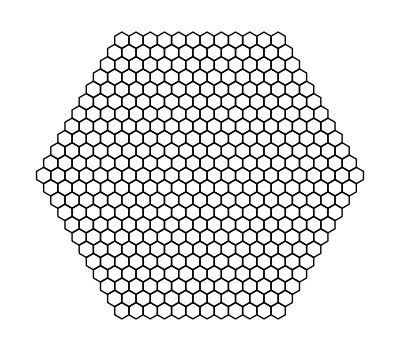

```mathematica
Show[Graphics[board[12]],AspectRatio->Automatic]
```

```mathematica
p[x_,y_]:={2Sqrt[3]/2 x-y Sqrt[3]/2,1.5y }
p[{x_,y_}]:=p[x,y]

board[nn_]:={Table[hex[i,j],{j,2,nn+1},{i,2,nn-1+j}],
	Table[hex[i,j],{j,nn+2,2nn},{i,j-nn+1,2nn}]}

hex[x_,y_]:={
	Line[{p[x,y]+{-Sqrt[3]/2,-1/2},p[x,y]+{-Sqrt[3]/2,1/2},p[x,y]+{0,1},p[x,y]+{Sqrt[3]/2,1/2},p[x,y]+{Sqrt[3]/2,-1/2},p[x,y]+{0,-1},p[x,y]+{-Sqrt[3]/2,-1/2}}]}
```

```mathematica
filledhex[{x_,y_}]:={
	Polygon[{p[x,y]+{-Sqrt[3]/2,-1/2},p[x,y]+{-Sqrt[3]/2,1/2},p[x,y]+{0,1},p[x,y]+{Sqrt[3]/2,1/2},p[x,y]+{Sqrt[3]/2,-1/2},p[x,y]+{0,-1},p[x,y]+{-Sqrt[3]/2,-1/2}}]}
```

```mathematica
box[nn_,k_]:=Module[{},n=2 nn-1;m=2 nn-1;A=Table[If[i==1||i==n+2||j==1||j==m+2||Abs[i-j]≥nn,1,0],{i,n+2},{j,m+2}];For[i=1,i≤k,i++,g={1,1};While[A⟦Sequence@@g⟧==1,g={RandomInteger[{2,n+1}],RandomInteger[{2,m+1}]}];A=ReplacePart[A,1,g]];chec[A];If[Length[B]==1,pic1=Graphics[{board[nn],(filledhex[#1]&)/@Select[Position[A,1],1<#1⟦1⟧<n+2&&1<#1⟦2⟧<m+2&&Abs[#1⟦1⟧-#1⟦2⟧]<nn&]}];pic2=Graphics[{AbsoluteThickness[2],RGBColor[0,0,1],Line[(p[#1]&)/@B⟦1⟧],Text[Style["S",Large],p[B⟦1,1⟧]],Text[Style["F",Large],p[Last[B⟦1⟧]]]}];p1=Show[pic1,AspectRatio->Automatic,ImageSize->{35 (2 n-1),35 (2 n-1)}];p2=Show[{pic1,pic2},AspectRatio->Automatic,ImageSize->{35 (2 n-1),35 (2 n-1)},PlotRange->All];Print[Show[GraphicsRow[{p1,p2},DisplayFunction->$DisplayFunction,ImageSize->{36 (2 n-1),18 (2 n-1)}]]]]]
```

```mathematica
chec[A_]:=Module[{},
		B={};
		stack=Map[{#}&,Position[A,0]];
    While[Length[stack]>0&&Length[B]<2,
			path=Last[stack];
			stack=Drop[stack,-1];
			last=Last[path];
			nbrs=Select[{last+{1,0},last+{0,1},last+{-1,0},last+{0,-1},last+{1,1},last+{-1,-1}},!MemberQ[path,#]&&A[[Apply[Sequence,#]]]==0&];
			If[Length[nbrs]==0,If[Length[path]==Length[Position[A,0]],AppendTo[B,path]]];
			stack=Join[stack,Map[Join[path,f[last,#]]&,nbrs]]]]
```

```mathematica
f[a_,b_]:=Module[{},
		z=1;
		While[A[[Apply[Sequence,b+z(b-a)]]]==0&&!MemberQ[path,b+z(b-a)],z++];
		Table[b+y(b-a),{y,0,z-1}]]
```

```mathematica
For[ll=1,ll<=100000,ll++,box[4,6]]
```

$Aborted

## 4

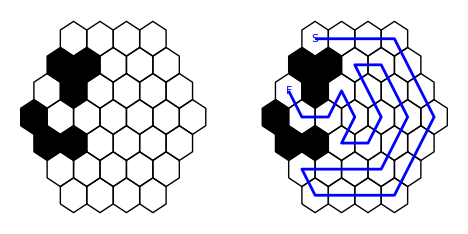

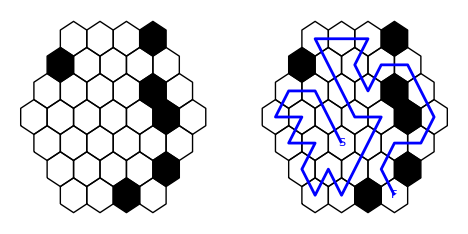

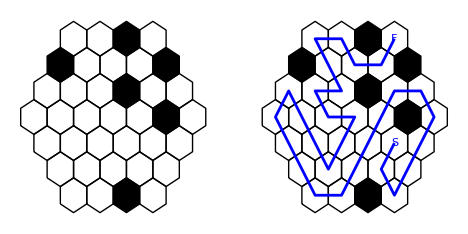

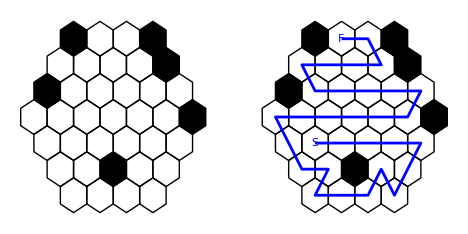

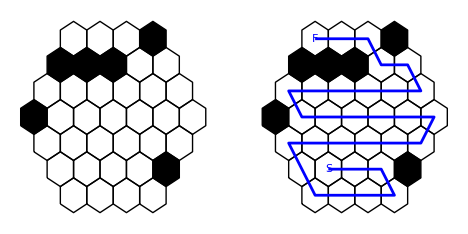

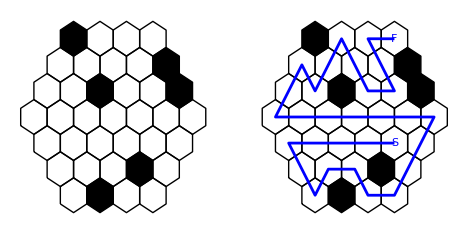

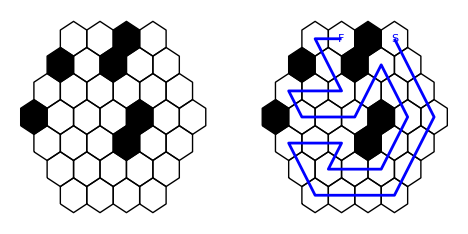

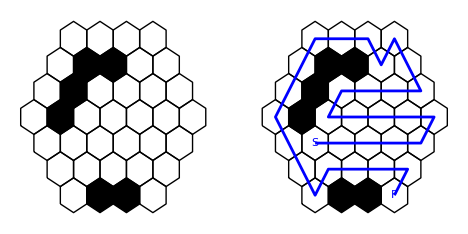

-Graphics-

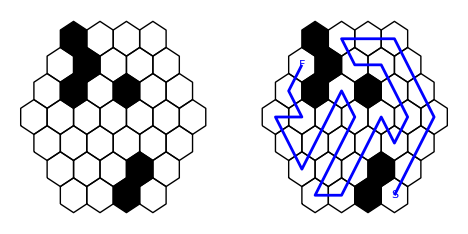

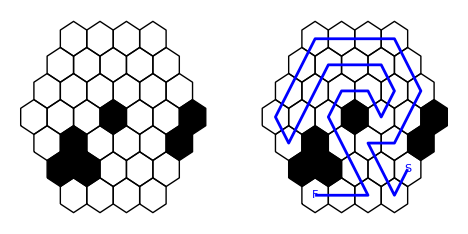

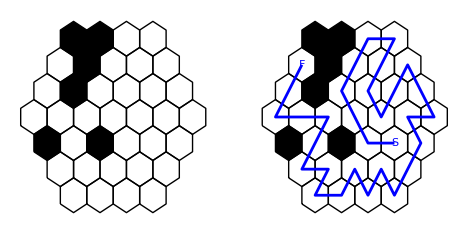

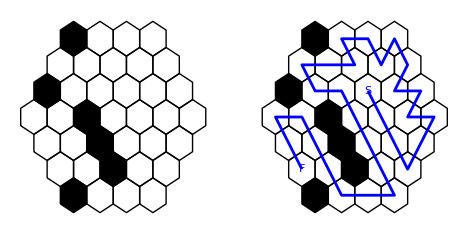

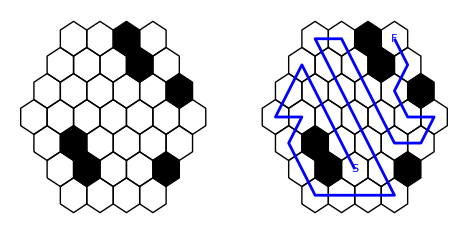

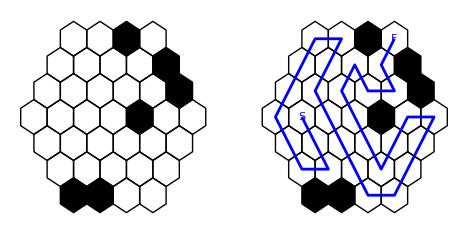

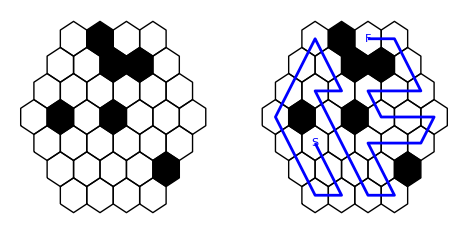

## 5